```mathematica
<<Local`QFTToolKit`
<<PhysicalConstants`
<<Units`
```

```mathematica
DeclareIndexFlavor[{dotted,Orange}]
DeclareIndexFlavor[{undotted,Blue}]
DefineTensorShortcuts[{{η,v,D,F,Λ,H},1},
{{σ},3}
]
AddBaseIndex[{dotted,{1,2}}]
AddBaseIndex[{undotted,{1,2}}]
```

{{0,1,2,3},{field,{1,2,3,4}},{feyn,{1,2,3,4,5}},{space,{1,2,3}},{timespace,{0,1}},{groupR,{1,2,3}},{gaugeG,{1,2,3}},{dotted,{1,2}}}

{{0,1,2,3},{field,{1,2,3,4}},{feyn,{1,2,3,4,5}},{space,{1,2,3}},{timespace,{0,1}},{groupR,{1,2,3}},{gaugeG,{1,2,3}},{dotted,{1,2}},{undotted,{1,2}}}

Lecture 2010.09.24

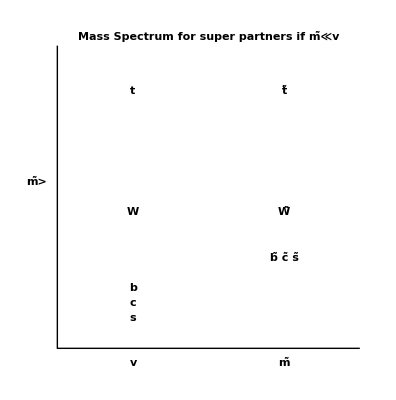
If there were 2 mass scales {m̃,v}→{mass of super partners, vacuum expectation value VEV}then the two conditions 
→ m̃≪v and m̃≫v can be excluded.
◆If m̃≪v the mass spectrum would look like: -Graphics-
Mass spectrum of super partners > SM particles at low mass.  This is would not be allowed by SUSY.

```mathematica
PR1["If there were 2 mass scales ",{m̃,v}->{"mass of super partners, vacuum expectation value VEV"},"then the two conditions ",Yield,
m̃≪v,and,m̃≫v," can be excluded.",
next,"If ",m̃≪v," the mass spectrum would look like: ",
Graphics[{Thick,Line[{{1,0},{0,0},{0,1}}],{Text[Style["Mass Spectrum for super partners if m̃≪v",Larger,Bold],{.5,1.03}],Text[Style["v",Large,Bold],{.25,-.05}]
,Text[Style["m̃",Large,Bold],{.75,-.05}]
,Text[Style["t",Large,Bold],{.25,.85}]
,Text[Style["t̃",Large,Bold],{.75,.85}]
,Text[Style["W",Large,Bold],{.25,.45}]
,Text[Style["W̃",Large,Bold],{.75,.45}]
,Text[Style["b",Large,Bold],{.25,.20}]
,Text[Style["c",Large,Bold],{.25,.15}]
,Text[Style["s",Large,Bold],{.25,.10}]
,Text[Style["b̃ c̃ s̃",Large,Bold],{.75,.30}]
,Text[Style["m̃>",Large,Bold],{-.07,.55}]
}
}
],
NL,"Mass spectrum of super partners > SM particles at low mass.  This is would not be allowed by SUSY."
];
```

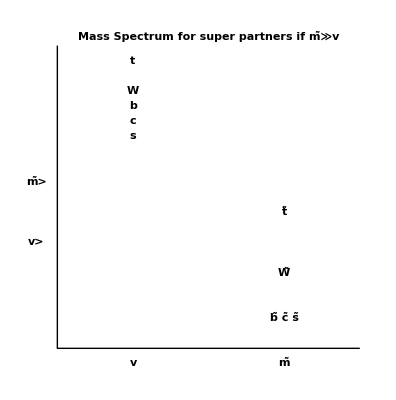
If m̃≫v the mass spectrum would look like: -Graphics-
Mass spectrum of super partners < SM particles.  This also would not be allowed by SUSY.

```mathematica
PR1["If ",m̃≫v," the mass spectrum would look like: ",
Graphics[{Thick,Line[{{1,0},{0,0},{0,1}}],{Text[Style["Mass Spectrum for super partners if m̃≫v",Larger,Bold],{.5,1.03}],Text[Style["v",Large,Bold],{.25,-.05}]
,Text[Style["m̃",Large,Bold],{.75,-.05}]
,Text[Style["t",Large,Bold],{.25,.95}]
,Text[Style["t̃",Large,Bold],{.75,.45}]
,Text[Style["W",Large,Bold],{.25,.85}]
,Text[Style["W̃",Large,Bold],{.75,.25}]
,Text[Style["b",Large,Bold],{.25,.80}]
,Text[Style["c",Large,Bold],{.25,.75}]
,Text[Style["s",Large,Bold],{.25,.70}]
,Text[Style["b̃ c̃ s̃",Large,Bold],{.75,.10}]
,Text[Style["m̃>",Large,Bold],{-.07,.55}]
,Text[Style["v>",Large,Bold],{-.07,.35}]
}
}
],
NL,"Mass spectrum of super partners < SM particles.  This also would not be allowed by SUSY."
]
```

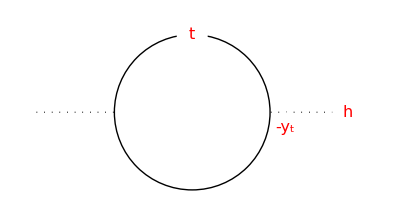
Calculation of radiative correction of Higgs get back quadratic divergence 
The self-energy diagram from :-Graphics-
⇒ mass correction  ⟶ δμ^2≈(3 (m̃)^2 y_t^2)/(8 π^2)
→ This reintroduces fine tuning problem and implies m̃≈v
● Supersymmetry breaking is tricky.  Given a potential V→UnderBar[∑]_{A}[(D_A^A)^2]+UnderBar[∑]_{a}[(F_a^a)^2] where (F_a^a)^2→Abs[UnderBar[∂]_A[W]] and D_A^A→g.(A_i^i)^-1.T_ij^ij.A_j^j
The signal for supersymmetry breaking is ⟨F_a^a⟩≠0 and/or ⟨D_A^A⟩≠0

```mathematica
scale=1;
MidArrow[xy_]:={Arrow[{xy[[1]],(xy[[1]]+xy[[2]])/2}],Line[{(xy[[1]]+xy[[2]])/2,xy[[2]]}]};
TextOver[text_,xy_]:={White,Disk[xy,0.2scale],
Text[Style[text,FontSize->16,Red],xy]};
Graphics121[x_]:=Graphics[{Thick,Black,
Circle[{0,0},scale],
Dotted,Line[{{-2 scale,0},{-1 scale,0}}],
Line[{{2 scale,0},{1 scale,0}}],
TextOver[x,{1.2,-.2 scale}],
TextOver[h,{2,0 scale}],
TextOver[t,{0,1 scale}]
}
];
Graphics20[x_]:=Graphics[{Thick,Black,Dotted,
Circle[{0,0},scale],
Line[{{-scale,-1.2 scale},{ 0,-scale}}],
Line[{{0,-scale},{ scale,-1.2 scale}}],
TextOver[x,{0,-1.3 scale}]
}
];
PR1["Calculation of radiative correction of Higgs get back quadratic divergence ",
NL,"The self-energy diagram from :",
Graphics121[-Subscript[y, t]],Imply,
"mass correction ",yield,
δμ^2≈(3 Subscript[y, t]^2)/(8 π^2)(m̃)^2,Yield,
"This reintroduces fine tuning problem and implies ",
m̃≈v,
New,"Supersymmetry breaking is tricky.  Given a potential ",
tmpV=V->xSum[Fd[a]^2,{a}]+xSum[Dd[A]^2,{A}],
" where ",
Fd[a]^2->Abs[xPartialD[W,A]],and,
Dd[A]->g.(Ad[i]^-1).Tdd[i,j].Ad[j],
NL,"The signal for supersymmetry breaking is ",
BraKet[Fd[a]]≠0," and/or ",BraKet[Dd[A]]≠0
];
```

```mathematica
PR1["Theorem: DimoPoulos-Georgi (1981): 
For the supersymmetric standard model (3.2.1 symmetry) SUSY with particles ",
{Q,u,D,L,⋯},
NL,"Assuming: 
1. Gauge group->3.2.1
2. Dominant SUSY breaking is at tree level 
3. SUSY is global
4. Space-time is 4D
Then ∃ ũ light with m_u->5Mev
and d̃ light with m_d->8Mev
,i.e, light super partners
",
CG["Can prove this theorem with current class material."],
NL,"This theorem shows that if these conditions exist then these light particles should exist.  But they have not been seen."
];
```

Theorem: DimoPoulos-Georgi (1981): 
For the supersymmetric standard model (3.2.1 symmetry) SUSY with particles {Q,u,D,L,⋯}
Assuming: 
1. Gauge group->3.2.1
2. Dominant SUSY breaking is at tree level 
3. SUSY is global
4. Space-time is 4D
Then ∃ ũ light with m_u->5Mev
and d̃ light with m_d->8Mev
,i.e, light super partners
Can prove this theorem with current class material.
This theorem shows that if these conditions exist then these light particles should exist.  But they have not been seen.

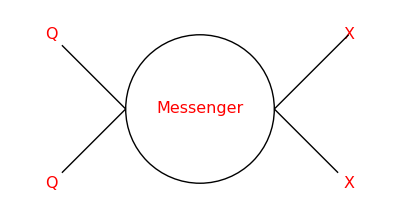
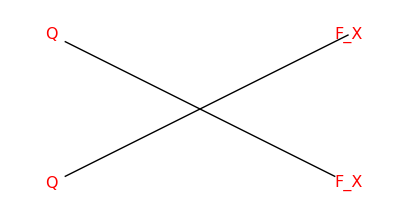
There have been attempts to spontaneously break super-symmetry by eliminating om of these assumptions.  These methods rely on three sectors: the original SUSY 3.2.1 sector, a messenger sector, and the broken SUSY sector.
SUSY 3.2.1 {Q,u,D,m̃,⋯} | Messengers | Broken SUSY
at primodial scale Λ_SUSY∼√F
 | New group G' | 
 | φφ̄ | gauge mediation
 | super-gravity | gravity mediation
 | extra-dimensions | 
Diagramically we have:
-Graphics-
→ Integrate out messenger loop given that energy E >> m_s messenger scale:
→ -Graphics-

```mathematica
PR1["There have been attempts to spontaneously break super-symmetry by eliminating om of these assumptions.  These methods rely on three sectors: the original SUSY 3.2.1 sector, a messenger sector, and the broken SUSY sector.",
NL,
Grid[{{"SUSY 3.2.1 {Q,u,D,m̃,⋯}","Messengers","Broken SUSY
at primodial scale Λ_SUSY∼√F"},{,"New group G'",},
{,"φφ̄","gauge mediation"},
{,"super-gravity","gravity mediation"},
{,"extra-dimensions",}},
Frame->All],
NL,"Diagramically we have:",
NL,
Graphics[{Thick,Black,
Circle[{0,0},1],
Line[{{-2,-1 },{ -1,0}}],TextOver["Q",{-2,-1}],
Line[{{-2,1 },{ -1,0}}],TextOver["Q",{-2,1}],
Line[{{2,-1 },{ 1,0}}],TextOver["X",{2,1}],
Line[{{2,1 },{ 1,0}}],TextOver["X",{2,-1}],

TextOver["Messenger",{0,0}]
}
],Yield,
"Integrate out messenger loop given that energy E >> m_s messenger scale:",Yield,
Graphics[{Thick,Black,
Line[{{-2,-1 },{ -0,0}}],TextOver["Q",{-2,-1}],
Line[{{-2,1 },{ -0,0}}],TextOver["Q",{-2,1}],
Line[{{2,-1 },{ 0,0}}],TextOver["F_X",{2,1}],
Line[{{2,1 },{ 0,0}}],TextOver["F_X",{2,-1}]
}
]
]
```

```mathematica
PR1["Example of Gauge mediation: ",W->X.Hd[u].Hd[d]
]
```

Example of Gauge mediation: W→X.H_u^u.H_d^d

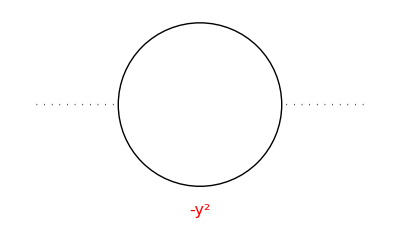
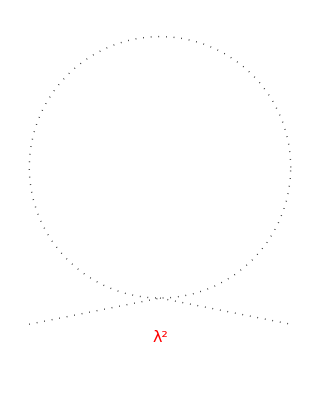
The following is a Toy model presentation to show some features of SUSY.  Assume fields {A,ψ_α^α} where A is a scalar field and ψ_α^α is a fermionic field.  We take the interaction Lagrangian (with coupling parameters {y,λ}) to be
→ ℒ_int→-A y ψ.ψ-λ^2 (A^†.A)^2
and the mass Lagrangian to be
→ ℒ_mass→A^†.A m_A^2-m_ψ (ψ.ψ+(ψ.ψ)^†)
The self-energy diagram from :-A y ψ.ψ ⟶ -Graphics-
The self-energy diagram from :-λ^2 (A^†.A)^2 ⟶ -Graphics-
These self-energy terms cancel if λ==y for λ≫m

```mathematica
PR1["The following is a Toy model presentation to show some features of SUSY.  Assume fields ",
tmp={A,ψd[α]}," where ",tmp[[1]]," is a scalar field and ",tmp[[2]]," is a fermionic field.  We take the interaction Lagrangian (with coupling parameters {y,λ}) to be",Yield,
tmpLi=Subscript[ℒ, int]->-y A (ψ.ψ)-λ^2(SuperDagger[A].A)^2,
NL,"and the mass Lagrangian to be",Yield,
tmpLm=Subscript[ℒ, mass]->Subscript[m, A]^2 SuperDagger[A].A-Subscript[m, ψ](ψ.ψ+SuperDagger[(ψ.ψ)]),

NL,"The self-energy diagram from :",tmpLi[[2,2]],yield,
Graphics20[λ^2],
NL,"These self-energy terms cancel if ", λ==y," for ",λ≫m
];
```

```mathematica
PR1["From the Wess-Zumino model:
Suppose the potential is restricted to quartic terms ",tmpV=Pot[ψd[1],ψd[2]]->{ψd[i]^4,⋯},
NL,"If there is a symmetry in ",
tmpψ=ψ->{ψd[1],ψd[2]}∍Potential[ψd[1],ψd[2]]->(Sum[ψd[$]^2,{$,1,2}])^2,
NL,"Then there will be a reduction in the number of coefficients."
];
```

From the Wess-Zumino model:
Suppose the potential is restricted to quartic terms Pot[ψ_1^1,ψ_2^2]→{(ψ_i^i)^4,⋯}
If there is a symmetry in ψ→{ψ_1^1,ψ_2^2}∍Potential[ψ_1^1,ψ_2^2]→((ψ_1^1)^2+(ψ_2^2)^2)^2
Then there will be a reduction in the number of coefficients.

```mathematica
subBar={Conjugate[OverBar[a_]]->a,Conjugate[Tensor[a__]]->OverBar[Tensor[a]],OverBar[OverBar[a_]]->a}
PR1["Determine symmetry group for ",{A,Subscript[ψ, α]},
NL,"Change due to incremental Lorentz transformation:",
Column[
tmpL={δ[A]->√2 ξu[undotted@α]ψd[undotted@α],δ[ψd[undotted@α]]->√2 I σudd[μ,undotted@α,dotted@α] OverBar[ξu[dotted@α]] xPartialD[A,μ]}
],
New,"Lorentz transformation for spinors with Weyl basis.",Yield,
subD=Subscript[ψ, Dirac]->{{ηd[undotted@α]},{OverBar[χu[dotted@α]]}};
MapAt[MatrixForm,subD,2],yield,
subD1=Map[xPartialD[#,μ]&,subD]//.xPartialDExpand[{}];
MapAt[MatrixForm,subD1,2],
NL,"The definitions of γ[σ]: ",
subγ2σ={γu[μ]->{{0,σu[μ]},{OverBar[σu[μ]],0}},γu[0]->{{0,σu[0]},{σu[0],0}},σu[0]->1};Yield,
Map[MapAt[MatrixForm,#,2]&,subγ2σ]," where ",
{σu[μ]->{σu[0],σ⃗},OverBar[σu[μ]]->{σu[0],-σ⃗},σu[0]->{{1,0},{0,1}}},
NL,"Dirac and Weyl kinetic energy terms are related ",Yield,
tmp=I OverBar[Subscript[ψ, Dirac]].γu[μ].xPartialD[Subscript[ψ, Dirac],μ],Yield,
tmp=tmp/.OverBar[a_]:>ConjugateTranspose[a].γu[0],Yield,
tmp=tmp/.subγ2σ/.σu[0]->1,Yield,
tmp=tmp/.Dot->xDot,Yield,
tmp=tmp/.subD1/.subD/.subBar,Yield,
tmp=tmp/.xDot[a__]:>NCxDotMatrixMultiply1[a],back,
"In the notes this seems to have the interpretation ",
I OverBar[ψd[dotted@α]].OverBar[σuuu[μ,dotted@α,undotted@α]].xPartialD[ψd[undotted@α],μ],implyQ,
ψd[undotted@α]->subD[[2]],and,
OverBar[ψd[dotted@α]]->SuperDagger[subD[[2]]]/.subDaggerCT/.subBar,and,
" the α indices of ",
OverBar[σuuu[μ,dotted@α,undotted@α]],
" refer to the individual elements of the σ's.",
note,"For this to work out properly with the off-diagonal components of the σ the ",OverBar[ψd[dotted@α]]," needs to be defined with ",γu[0]
];
```

{OverBar[a_]^*→a,a__^*→ā,OverBar[OverBar[a_]]→a}

Determine symmetry group for {A,ψ_α}
Change due to incremental Lorentz transformation:δ[A]→√2 ξ_α^α ψ_α^α
δ[ψ_α^α]→ⅈ √2 OverBar[ξ_α^α] σ_μαα^μαα UnderBar[∂]_μ[A]
● Lorentz transformation for spinors with Weyl basis.
→ ψ_Dirac→(η_α^α
OverBar[χ_α^α]) ⟶ UnderBar[∂]_μ[ψ_Dirac]→(UnderBar[∂]_μ[η_α^α]
UnderBar[∂]_μ[OverBar[χ_α^α]])
The definitions of γ[σ]: 
→ {γ_μ^μ→(0 | σ_μ^μ
OverBar[σ_μ^μ] | 0),γ_0^0→(0 | σ_0^0
σ_0^0 | 0),σ_0^0→1} where {σ_μ^μ→{σ_0^0,σ⃗},OverBar[σ_μ^μ]→{σ_0^0,-σ⃗},σ_0^0→{{1,0},{0,1}}}
Dirac and Weyl kinetic energy terms are related 
→ ⅈ OverBar[ψ_Dirac].γ_μ^μ.UnderBar[∂]_μ[ψ_Dirac]
→ ⅈ (ψ_Dirac)^†.γ_0^0.γ_μ^μ.UnderBar[∂]_μ[ψ_Dirac]
→ ⅈ (ψ_Dirac)^†.{{OverBar[σ_μ^μ],0},{0,σ_μ^μ}}.UnderBar[∂]_μ[ψ_Dirac]
→ ⅈ xDot[(ψ_Dirac)^†,{{OverBar[σ_μ^μ],0},{0,σ_μ^μ}},UnderBar[∂]_μ[ψ_Dirac]]
→ ⅈ xDot[{{OverBar[η_α^α],χ_α^α}},{{OverBar[σ_μ^μ],0},{0,σ_μ^μ}},{{UnderBar[∂]_μ[η_α^α]},{UnderBar[∂]_μ[OverBar[χ_α^α]]}}]
→ {{ⅈ (OverBar[η_α^α].OverBar[σ_μ^μ].UnderBar[∂]_μ[η_α^α]+χ_α^α.σ_μ^μ.UnderBar[∂]_μ[OverBar[χ_α^α]])}} ⟵In the notes this seems to have the interpretation ⅈ OverBar[ψ_α^α].OverBar[σ_μαα^μαα].UnderBar[∂]_μ[ψ_α^α] ?⇒ ψ_α^α→{{η_α^α},{OverBar[χ_α^α]}} and OverBar[ψ_α^α]→{{OverBar[η_α^α],χ_α^α}} and  the α indices of OverBar[σ_μαα^μαα] refer to the individual elements of the σ's.
⌘For this to work out properly with the off-diagonal components of the σ the OverBar[ψ_α^α] needs to be defined with γ_0^0

```mathematica
PR1[
New,"Toy Lagrangian ignore higher order terms",Yield,
tmpLkin=Subscript[ℒ, kin]->xPartialDu[SuperDagger[A],μ].xPartialD[A,μ]+I ψ̄.OverBar[σu[μ]].xPartialD[ψ,μ],Yield,
tmpLmass=Subscript[ℒ, mass]->-Subscript[m, ψ](ψ.ψ+SuperDagger[(ψ.ψ)])-Subscript[m, A]^2 SuperDagger[A].A,Yield,
tmpLint=Subscript[ℒ, int]->-y (A.ψ.ψ+SuperDagger[(A.ψ.ψ)])-λ λ (SuperDagger[A].A)^2
]
```

● Toy Lagrangian ignore higher order terms
→ ℒ_kin→UnderBar[∂]^μ[A^†].UnderBar[∂]_μ[A]+ⅈ ψ̄.OverBar[σ_μ^μ].UnderBar[∂]_μ[ψ]
→ ℒ_mass→-A^†.A m_A^2-m_ψ (ψ.ψ+(ψ.ψ)^†)
→ ℒ_int→-λ^2 (A^†.A)^2-y (A.ψ.ψ+(A.ψ.ψ)^†)